```mathematica
ClearSystemCache[]
(* Get the gerneral solution *)
(*DSolve[{T'[x]==-Q/kA},T[x],x]*)



k = 0.5;
(* W/m2K using water *)

L = 0.01;
(* cm  *)

A = 1;
(* 1 meter ^2  *)

R = L/(k*A);
(* Resistance  *)

(* Temperature on one side of wall *)
Subscript[T, 0]= 50;

(* Temperature on the other side of the wall *)
Subscript[T, 1]=30;

Q = (Subscript[T, 0]-Subscript[T, 1])/R

(* Watt5s *)
FLUX = Q/A
eqn = NDSolve[{T'[x]==-Q/k*A, T[0]==Subscript[T, 0]},T,{x,0,L}]
```

1000.

1000.

DSolve::dsvar: 0 cannot be used as a variable.

DSolve[{T'[x]==-2000.,T[0]==50},T,{x,0,0.01}]

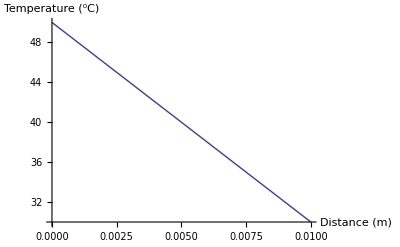

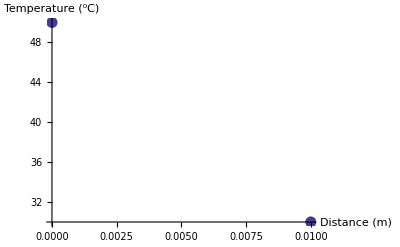

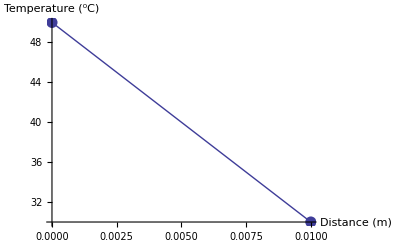

```mathematica
(*Plot1 = Plot [Subscript[T, 0] +x/L*(Subscript[T, 1]-Subscript[T, 0]), {x,0,L},PlotRange->{{0,.01},{30,50}},AxesLabel->{"Distance (m)","Temperature (^0C)"}]*)
Plot1 = Plot [eqn, {x,0,L},PlotRange->{{0,.01},{30,50}},AxesLabel->{"Distance (m)","Temperature (^0C)"}]

Plot2=ListPlot[{{0,50},{0.01,30}}, PlotStyle->{AbsolutePointSize[8]}, AxesLabel->{"Distance (m)","Temperature (^0C)"}]

Show[Plot1, Plot2]
```